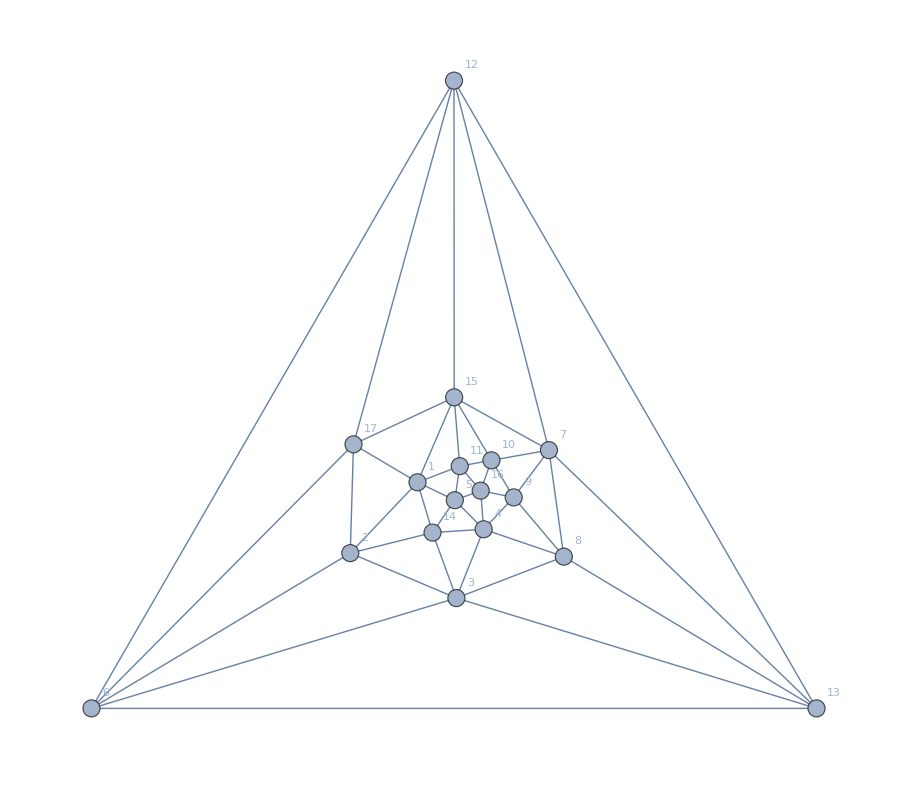

```mathematica
plantri8
```

```mathematica
EmbedGraphInPlantri8Bis[assoc_,key_]:=Block[{val=assoc[key], sets, reference={12,13,7,15,17}, g, sub},
sets=val["vertexsets"];
g=VertexDelete[ Graph[plantri[[8]]],14];
g=EdgeDelete[ g,{7<->13,13<->12,12<->17,17<->15,15<->7}];
Table[If[Length[s]>1,
g=VertexContract[g,Table[reference[[v]],{v,s}]]
], {s,sets}];
sub=val["graph"];
Table[
g=EdgeAdd[g,{reference[[First[sets[[e[[1]]]]]]]<->reference[[First[sets[[e[[2]]]]]]]}],{e,EdgeList[sub]}];

g
]
```

```mathematica
Table[k->ChromaticPolynomial[EmbedGraphInPlantri8[allGraphs5,k],4],{k,allGraphs5AtomKeys}]
```

{29524→0,29525→240,29527→144,29533→480,29537→336,29551→264,29560→744,29605→144,29608→0,29633→240,29767→240,29768→336,29797→240,29857→336,29888→264,30253→264,30262→696,30334→192,30496→384,30586→264,31711→216,31714→72,31738→192,31954→192,31984→96,32441→480,32684→288,36085→216,36086→192,36112→192,36166→72,36194→96,36817→312,36898→120,38281→168,38308→216,39014→384,49207→264,49208→384,49210→192,49216→696,49220→264,49963→504,49972→624,51475→312,51478→120,52232→432,56011→480,56012→288,56770→432,58288→384,59048→384}

```mathematica
ShowGraph5Least[29608]
```

```mathematica
Graph[plantri8,VertexLabels->"Name",GraphLayout->"LayeredDigraphEmbedding"]//PlanarGraphQ
```

True

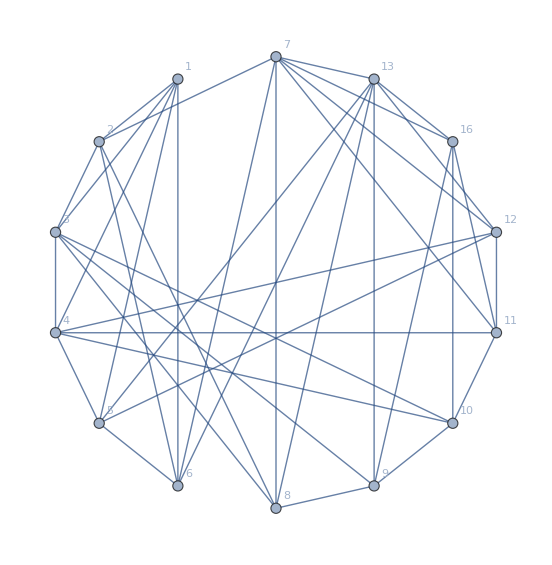

```mathematica
Graph[EmbedGraphInPlantri8[allGraphs5,29608],VertexLabels->"Name",GraphLayout->"CircularEmbedding"]
```

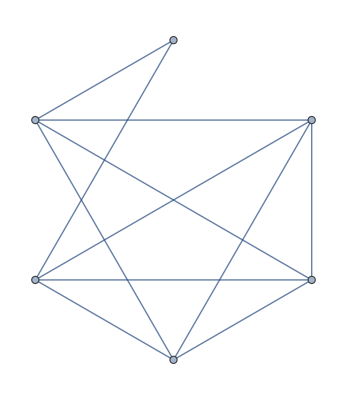

```mathematica
g=CompleteGraph[5];g=EdgeDelete[g,1<->2];g=EdgeAdd[g,{1<->6,6<->2}]
```

```mathematica
ChromaticPolynomial[g,x]
```

-42 x+107 x^2-103 x^3+48 x^4-11 x^5+x^6

```mathematica
VertexCount[EmbedGraphInPlantri8[allGraphs5,29608]]
```

14

```mathematica
Map[VertexCount,SimpleMinors[EmbedGraphInPlantri8[allGraphs5,29608]]]
```

{14,14,14,14,14,14,14,14,14,14,14,14,13,13,13,13,13,13,13,13,13,13,13,13}

```mathematica
FindK33[g_]:=Module[{vertexsets=Subsets[VertexList[g],{6}],sub},
Table[
sub=Subgraph[g,set];
If[IsomorphicGraphQ[sub,CompleteGraph[{3,3}]],
Print[set]
]
,{set,vertexsets}
];
Length[vertexsets]
]
```

```mathematica
FindK33[EmbedGraphInPlantri8[allGraphs5,29608]]
```

3003

```mathematica
FindK5[g_]:=Module[{vertexsets=Subsets[VertexList[g],{5}],sub},
Table[
sub=Subgraph[g,set];
If[IsomorphicGraphQ[sub,CompleteGraph[5]],
Print[set]
]
,{set,vertexsets}
];
Length[vertexsets]
]
```

```mathematica
FindK5[EmbedGraphInPlantri8[allGraphs5,29608]]
```

2002

```mathematica
done=0;todo=0;With[{g=EmbedGraphInPlantri8[allGraphs5,29608]},
With[{target=Subsets[EdgeList[g],{6}]},
todo=Length[target];
PrintTemporary[Dynamic[done]," ",ProgressIndicator[Dynamic[done/todo]]," ",todo];
First[ReverseSort[Table[done++;{Length[First[FindClique[EdgeContract[g,e]]]],e},{e,target}]]]
]]
```

$Aborted

```mathematica
done=0;todo=0;With[{g=EmbedGraphInPlantri8[allGraphs5,29608]},
With[{target=Subsets[EdgeList[g],{7}]},
todo=Length[target];
PrintTemporary[Dynamic[done]," ",ProgressIndicator[Dynamic[done/todo]]," ",todo];
First[ReverseSort[Table[done++;{Length[First[FindClique[EdgeContract[g,e]]]],e},{e,target}]]]
]]
```

{4,{13<->16,7<->8,7<->11,7<->16,12<->13,12<->7,13<->7}}

```mathematica
EdgeCount[EmbedGraphInPlantri8[allGraphs5,29608]]
```

```mathematica
38l
```

```mathematica
done=0;
todo=0;
Block[{g=EmbedGraphInPlantri8[allGraphs5,29608],pos,current},
With[{target=Subsets[EdgeList[g],{28}]},
todo=Length[target];
PrintTemporary[Dynamic[done]," ",ProgressIndicator[Dynamic[done/todo]]," ",todo];
For[pos=1,pos≤todo, pos++,
current=target[[pos]];
done++;
If[Length[First[FindClique[EdgeContract[g,current]]]]>4,
Print[current, "  ", First[FindClique[EdgeContract[g,e]]]];
Goto[ok]
]
];
];
Label[ok];
]
```

$Aborted

```mathematica
Table[StirlingS2[38,k],{k,38}]
```